# Chapter 5 - Problem 3

Plot the transmission coefficient as a function of the incoming energy for an electron going through the potential described by
V(x) = λ_1δ(x) + λ_2δ(x-L)
where λ_1 = 1 eV.nm and λ_2 = 1.2 eV.nm and L = 3 nm

In this problem, you’re given the λ values. i.e. you know the strength of each delta potential. However, you will see that sometimes you have to flip the sign of the given λ. In this problem, you do not. Because you are asked to plot the transmission coefficient. 
In problem 4, we’ll see that we have to flip the λ.

```mathematica
Clear["Global`*"]
(* Constants *)
e = 1.60217 * 10^-19; (* 1 electron volt(ev) = e Joules *)
h = 6.62607004 * 10^-34 ;(* planck's constant *)
m = 9.10938 * 10^-31; (* effective mass of an electron *)
ℏ = h/(2*Pi);
alpha = Sqrt[(2*m*e)/ℏ^2] * 10^-9;
```

```mathematica
(*In this problem, we have delta potentials. We only need the PP matrix and the Pdelta matrix.*)
PP[kx_,l_] = MatrixExp[-I*kx*l*PauliMatrix[3]];
Pdelta[λ_] = {{1+(I*λ*alpha)/(2*Sqrt[en]), (I*λ*alpha)/(2*Sqrt[en])},{(-1 *I*λ*alpha)/(2*Sqrt[en]),1 - (I*λ*alpha)/(2 * Sqrt[en])}};
```

```mathematica
(* now we have to find our k values *)
λ1 = 1;
λ2 = 1.2;
L = 3;
k1 = alpha * Sqrt[en-λ1];
k2 = alpha * Sqrt[en-λ2];
(* Assuming that this is happening in a vacuum with 0 potential*)
kvacuum = alpha * Sqrt[en];
```

```mathematica
M = Pdelta[λ1].PP[kvacuum,L].Pdelta[λ2];
```

#### The transmission coefficient is given by: T = |1/M_11|^2

```mathematica
transmission = Abs[1/M[[1,1]]^2];
```

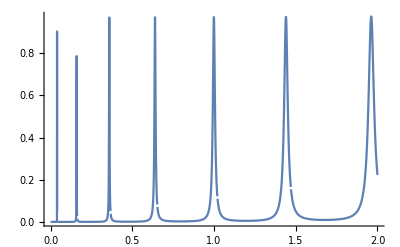

```mathematica
Plot[transmission,{en,0,2},PlotRange->All]
```

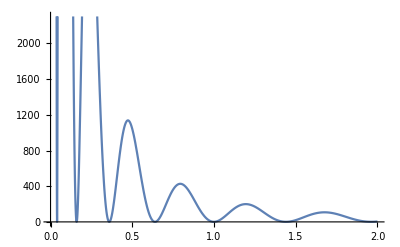

```mathematica
Plot[Abs[M[[1,1]]]^2,{en, 0,2}]
```

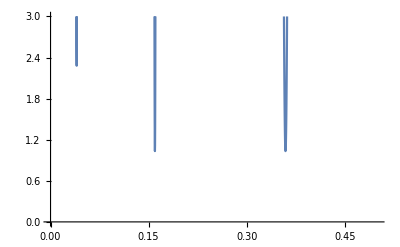

```mathematica
Plot[Abs[M[[1,1]]^2],{en,0,0.5}, PlotRange->{0,3}]
```